{{6,1.4},{2.5,2.16667},{9.5,2.16667}}

3.65306-0.75102 x+0.062585 x^2

{{6,0},{1.5,1.1},{11,1.1}}

1.90667-0.611111 x+0.0488889 x^2

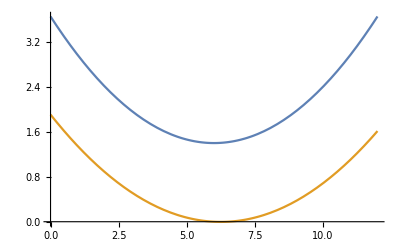

```mathematica
topData = {{6,4.2/3},{2.5,6.5/3},{9.5,6.5/3}}
topCurve = Fit[topData, {1,x,x^2}, x]

bottomData = {{6,0/3},{1.5,3.3/3},{11,3.3/3}}
bottomCurve = Fit[bottomData, {1,x,x^2}, x]
Plot[{topCurve,bottomCurve},{x,0,12}]
```

```mathematica
loftFunc := (z/6)
surface1:=(1-loftFunc)bottomCurve+loftFunc*topCurves
```

```mathematica
Plot3D[surface1,{x,0,12},{z,-6.,6.}]
```

-Graphics3D-

```mathematica
data=Transpose[ImportString["9\t12\t15\t18\t21\t24\t27\t30
0.5\t1.03\t1.5\t1.75\t1.6\t1.15\t0.7\t0.3","TSV"]]
```

{{9,0.5},{12,1.03},{15,1.5},{18,1.75},{21,1.6},{24,1.15},{27,0.7},{30,0.3}}